# Infinite 3D medium, Isotropic Point Source, Henyey-Greenstein Scattering

## Exponential Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
Σt - extinction coefficient
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine
b - anisotropy parameter

### Namespace

```mathematica
Begin["inf3DisopointHGscatter`"]
```

inf3DisopointHGscatter`

## Util

```mathematica
SA[d_,r_]:=d Pi^(d/2)/Gamma[d/2+1] r^(d-1)
```

### Diffusion modes

```mathematica
diffusionMode[v_,d_,r_]:=(2 π)^(-d/2) r^(1-d/2) v^(-1-d/2) BesselK[1/2 (-2+d),r/v]
```

## Analytical solutions

### Fluence: exact solution

[Grosjean 1963 - A New Approximate One-Velocity Theory for Treating both Isotropic and Anisotropic Multiple Scattering Problems, p. 37]

#### 3-term expansion

```mathematica
ϕexactorder2[r_,Σt_,c_,g_]:=Exp[-r Σt]/(4 Pi r^2)+(c Σt)/(2 Pi^2 r)NIntegrate[u((-3 g u^2 (15 g (-1+c g)+4 u^2)+3 g u (-15 (-2+c) g (-1+c g)+(8-10 g+c (-4+5 g^2)) u^2) ArcTan[u]+(12 (-1+c) g u^2+4 u^4+15 (-1+c) c g^3 (3+u^2)-5 g^2 (-3+3 c-u^2) (3+u^2)) ArcTan[u]^2)/(u (45 (-1+c) c g^2 (-1+c g) u+3 c g (-4+4 c+5 g) u^3+4 u^5-c (12 (-1+c) g u^2+4 u^4+15 (-1+c) c g^3 (3+u^2)-5 g^2 (-3+3 c-u^2) (3+u^2)) ArcTan[u])))Sin[r Σt u],{u,0,Infinity},Method->"LevinRule"]
```

#### 4-term expansion

```mathematica
ϕexactorder3[r_,Σt_,c_,g_]:=Exp[-r Σt]/(4 Pi r^2)+(c Σt)/(2 Pi^2 r)NIntegrate[u((-g u^2 (-405 g u^2+108 u^4-105 c g^3 (15+4 u^2)-105 c g^4 (15+4 u^2)+105 c^2 g^5 (15+4 u^2)+g^2 (1575+15 (56+27 c) u^2+112 u^4))+g u (-108 (-2+c) u^4-135 g u^2 (6-3 c+2 u^2)+35 c g^4 (-90+45 c-54 u^2+12 c u^2-4 u^4)+105 c g^3 (-30-13 u^2+c (15+4 u^2))-105 c^2 g^5 (-30-13 u^2+c (15+4 u^2))+g^2 (-405 c^2 u^2+42 (75+65 u^2+12 u^4)+c (-1575-30 u^2+23 u^4))) ArcTan[u]+3 (36 (-1+c) g u^4+12 u^6+15 g^2 u^2 (3+u^2) (3-3 c+u^2)-105 (-1+c) c g^4 (5+3 u^2)+105 (-1+c) c^2 g^6 (5+3 u^2)-35 c g^5 (-3+3 c-u^2) (5+3 u^2)+g^3 (45 c^2 u^2 (3+u^2)-21 (5+3 u^2)^2+c (525+320 u^2+39 u^4))) ArcTan[u]^2)/(u (u (36 u^6+105 c^4 g^6 (15+4 u^2)-15 c^3 g^3 (-27 u^2+7 g (15+4 u^2)+7 g^2 (15+4 u^2)+7 g^3 (15+4 u^2))-3 c g (36 u^4-45 g u^2 (3+u^2)+7 g^2 (75+65 u^2+12 u^4))+c^2 g (-405 g u^2+108 u^4+105 g^3 (15+4 u^2)+35 g^4 (45+27 u^2+4 u^4)+g^2 (1575+435 u^2+112 u^4)))-3 c (36 (-1+c) g u^4+12 u^6+15 g^2 u^2 (3+u^2) (3-3 c+u^2)-105 (-1+c) c g^4 (5+3 u^2)+105 (-1+c) c^2 g^6 (5+3 u^2)-35 c g^5 (-3+3 c-u^2) (5+3 u^2)+g^3 (45 c^2 u^2 (3+u^2)-21 (5+3 u^2)^2+c (525+320 u^2+39 u^4))) ArcTan[u])))Sin[r Σt u],{u,0,Infinity},Method->"LevinRule"]
```

#### 5-term expansion

```mathematica
ϕexactorder4[r_,Σt_,c_,g_]:=Exp[-r Σt]/(4 Pi r^2)+(c Σt)/(2 Pi^2 r)NIntegrate[u((-g u^2 (-6480 g u^4+1728 u^6-4725 c^2 g^7 (21+11 u^2)-4725 c^2 g^8 (21+11 u^2)+4725 c^3 g^9 (21+11 u^2)-315 c g^6 (-15+15 c-4 u^2) (21+11 u^2)+16 g^2 u^2 (1575+15 (56+27 c) u^2+112 u^4)+15 c g^4 (6615+3486 u^2+443 u^4)+105 c g^5 (945+15 (33+16 c) u^2+64 c u^4)-15 g^3 (6615+210 (33+8 c) u^2+(1815+448 c) u^4))+g u (-1728 (-2+c) u^6-2160 g u^4 (6-3 c+2 u^2)+315 c^2 g^8 (-630+315 c-540 u^2+165 c u^2-82 u^4)+945 c^2 g^7 (-210-145 u^2-9 u^4+5 c (21+11 u^2))-945 c^3 g^9 (-210-145 u^2-9 u^4+5 c (21+11 u^2))+16 g^2 u^2 (-405 c^2 u^2+42 (75+65 u^2+12 u^4)+c (-1575-30 u^2+23 u^4))-105 c g^5 (16 c^2 u^2 (15+4 u^2)+c (945+15 u^2-208 u^4)-6 (315+270 u^2+41 u^4))+c g^4 (198450+137655 u^2+13500 u^4-53 u^6-15 c (6615+3486 u^2+443 u^4))+63 c g^6 (75 c^2 (21+11 u^2)-5 c (945+684 u^2+71 u^4)+6 (525+590 u^2+165 u^4+6 u^6))+15 g^3 (112 c^2 u^2 (15+4 u^2)+c (6615+3570 u^2+359 u^4)-18 (735+1015 u^2+393 u^4+33 u^6))) ArcTan[u]+3 (576 (-1+c) g u^6+192 u^8+240 g^2 u^4 (3+u^2) (3-3 c+u^2)-945 (-1+c) c^2 g^8 (35+30 u^2+3 u^4)+945 (-1+c) c^3 g^10 (35+30 u^2+3 u^4)-315 c^2 g^9 (-3+3 c-u^2) (35+30 u^2+3 u^4)-63 c g^7 (35+30 u^2+3 u^4) (15+15 c^2+9 u^2-2 c (15+2 u^2))+16 g^3 u^2 (45 c^2 u^2 (3+u^2)-21 (5+3 u^2)^2+c (525+320 u^2+39 u^4))+105 c g^6 (16 c^2 u^2 (5+3 u^2)+c (315+190 u^2-21 u^4)-3 (105+125 u^2+39 u^4+3 u^6))-3 g^4 (560 c^2 u^2 (5+3 u^2)-9 (35+30 u^2+3 u^4)^2+5 c (2205+2485 u^2+843 u^4+99 u^6))+c g^5 (-33075-28455 u^2-2285 u^4+951 u^6+3 c (11025+9485 u^2+1695 u^4+243 u^6))) ArcTan[u]^2)/(u (u (576 u^8+4725 c^5 g^10 (21+11 u^2)-105 c^4 g^6 (-16 u^2 (15+4 u^2)+45 g (21+11 u^2)+45 g^2 (21+11 u^2)+45 g^3 (21+11 u^2)+45 g^4 (21+11 u^2))+15 c^3 g^3 (432 u^4-112 g u^2 (15+4 u^2)+315 g^5 (21+11 u^2)+105 g^6 (63+54 u^2+11 u^4)+42 g^4 (315+207 u^2+22 u^4)-7 g^3 (-945-255 u^2+64 u^4)+g^2 (6615+3486 u^2+443 u^4))+3 c g (-576 u^6+720 g u^4 (3+u^2)-112 g^2 u^2 (75+65 u^2+12 u^4)+45 g^3 (735+1015 u^2+393 u^4+33 u^6))-c^2 g (6480 g u^4-1728 u^6+1575 g^5 (63+54 u^2+11 u^4)+945 g^6 (105+118 u^2+33 u^4)-16 g^2 u^2 (1575+435 u^2+112 u^4)+15 g^3 (6615+5250 u^2+1367 u^4)-5 g^4 (-19845-10458 u^2+351 u^4+448 u^6)))-3 c (576 (-1+c) g u^6+192 u^8+240 g^2 u^4 (3+u^2) (3-3 c+u^2)-945 (-1+c) c^2 g^8 (35+30 u^2+3 u^4)+945 (-1+c) c^3 g^10 (35+30 u^2+3 u^4)-315 c^2 g^9 (-3+3 c-u^2) (35+30 u^2+3 u^4)-63 c g^7 (35+30 u^2+3 u^4) (15+15 c^2+9 u^2-2 c (15+2 u^2))+16 g^3 u^2 (45 c^2 u^2 (3+u^2)-21 (5+3 u^2)^2+c (525+320 u^2+39 u^4))+105 c g^6 (16 c^2 u^2 (5+3 u^2)+c (315+190 u^2-21 u^4)-3 (105+125 u^2+39 u^4+3 u^6))-3 g^4 (560 c^2 u^2 (5+3 u^2)-9 (35+30 u^2+3 u^4)^2+5 c (2205+2485 u^2+843 u^4+99 u^6))+c g^5 (-33075-28455 u^2-2285 u^4+951 u^6+3 c (11025+9485 u^2+1695 u^4+243 u^6))) ArcTan[u])))Sin[r Σt u],{u,0,Infinity},Method->"LevinRule"]
```

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_HG_*"];
```

```mathematica
index[x_]:=Module[{data,c,mfp,g},
data=Import[x,"Table"];
mfp=data[[1,13]];
c=data[[2,3]];
g=data[[1,16]];
{c,mfp,g,data}];
simulations=index/@fs;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
mfps=Union[#[[2]]&/@simulations]
```

{0.3,1}

```mathematica
gs=Union[#[[3]]&/@simulations]
```

{-0.5,0.3,0.5,0.7}

```mathematica
numcollorders=inf3Disopointlinanisoscatter`simulations[[1]][[-1]][[2,13]];
```

## Compare Deterministic and MC

```mathematica
Clear[g]
```

### Mean Track Length

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set g","g = "<>ToString[#]:>(g=#;)&/@gs],Dynamic[g]}}
```

{{Set c,},{Set mfp,},{Set g,}}

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==g&][[4]];
meanTL=data[[-1]]
mfp/(1-c)
```

{Mean,track,length:,2.00001}

2.

### Fluence - Exact solution (1) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set g","g = "<>ToString[#]:>(g=#;)&/@gs],Dynamic[g]}}
```

{{Set c,},{Set mfp,},{Set g,}}

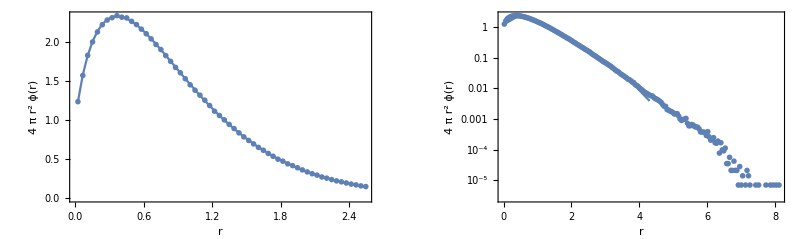

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==g&][[4]];
maxr=data[[2,5]];
dr=data[[2,7]];
pointsFluence=ppoints[data[[6]],dr,maxr];
exact1FluenceShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexactorder4[#[[1]],1/mfp,c,g]}]& /@pointsFluence[[1;;60]];
exact1Fluence=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexactorder4[#[[1]],1/mfp,c,g]}]& /@pointsFluence[[1;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1Fluence,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution - expansion order 2\nInfinite 3D, isotropic point source, Henyey-Greenstein scattering, fluence ϕ[r], c = "<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]<>", g = "<>ToString[g]]
```

## Close namespace

```mathematica
End[]
```